# Simulation of Contrast Losses due to Beam Divergence and AC Stark Effect

## (Using 2.7.2 and 4.1) Laser Beam Simulation

### Hermite-Gaussian Beam Simulation

This section defines the Hermite-Gaussian modes using eq. 2.12-2.15 of the Master’s thesis.

```mathematica
(* Define some  auxiliary functions *)
λ = c/fL;
zR = (π w0^2)/λ;   (*Rayleigh range*)
k = (2 π)/λ;     (*Wavenumber*)
ζ[z_] =z/zR;    (* Scaled z-coordinate zeta ζ *)
w[z_] = w0(1+ζ[z]^2)^(1/2);    (*waist as function of ζ*)
ψ[m_,n_,z_] = (1+m+n)ArcTan[ζ[z]];     (*Gouy phase as a function of HG orders m,n*)

(* Main equation for HG propgation, each mode is normalized to have total integrated power of 1 (integral of Abs[HG]^2 over x and y). For later ease of use, I explicitly separate out amplitude and phase *)
HGAmplitude[m_,n_,x_,y_,z_] = (2/π)^(1/2)√(1/(2^m m!))√(1/(2^n n!))1/w[z] HermiteH[m,√2 x/w[z]]HermiteH[n,√2 y/w[z]]Exp[- (x^2 + y^2)/(w0^2(1 +ζ[z]^2))];
HGPhase [m_,n_,x_,y_,z_]=k z + (ζ[z](x^2 + y^2))/(w0^2(1 +ζ[z]^2))-ψ[m,n,z];
HG[m_,n_,x_,y_,z_] = HGAmplitude[m,n,x,y,z]Exp[ⅈ HGPhase[m,n,x,y,z]];
```

### Set of Experimental Paramters

Here, nBragg is the Bragg order, NBloch is the number of Bloch oscillations, (m,n) is the order of the Hermite-Gaussian modes, w0 is the beam waist, ω0 is the D2 line transition frequency, c is the speed of light, Γ is the D2 line decay rate, ℏ is the Planck constant, mCs is the cesium mass, ωRecoil is the single-photon recoil frequency for cesium, v0 is the velocity with which the atoms are launched, and g is the gravitational acceleration.

```mathematica
(*Eval for real world constants and experimental parameters, all in SI units *)
evalExperiment = {nBragg->5,m ->0, n->0,w0->0.008,ω0->2 π 3 10^8/(852 10^-9),c-> 299792458,Γ-> 2 π 5.223 10^6,Δ-> 2π 40*10^9, ℏ -> 1.0546 10^-34, mCs -> 2.207 10^-25, ωRecoil ->  2 π 2066, v0->4.5,g->9.79};
(*Laser beam frequency and total laser power for Bloch oscillations *)
evalBeam={fL->351.72601 10^12,P ->0.382};
ev=Join[evalBeam,evalExperiment];
(* useful args for making plot *)
densityPlotArgs :=  Sequence[ColorFunction->"CMYKColors", PlotLegends->Automatic,PlotRange->All, PlotPoints->100, Frame->True];
z0=0.5; (* z0 is the position of the focus point for the upgoing beam. The retro-reflecting mirror is set to be at z=0 *)
```

```mathematica
NBloch=125; (* Number of Bloch oscillations *)
vph[n_]=(2 n ℏ k)/mCs; (* recoil velocity for n photon pairs *)
zoffset=-2; (* |zoffset| is the distance between the atoms at the first Bragg pulse and the retro-reflecting mirror *)
```

```mathematica
(* ETot is the total electric field (including the conterpropagating beam) *)
A1=1; 
A2=0;
ripples=10; (* sets the HG order *)
ETot[x_,y_,z_]=A1 HG[0,0,x,y,z+z0]+A2 HG [ripples,ripples,x,y,z+z0]+A1 HG[0,0,x,y,z-z0]+A2 HG [ripples,ripples,x,y,z-z0]/.ev;
```

The following function is used to implement intensity variations based on eq. 4.40 of the Master’s thesis.

```mathematica
a0=1 10^-3;
q=1/(50 10^-6);
zNoiseoffset=-4;
zRNoise=2;
Noise[x_,y_,z_]=Exp[(-q^2 (z-zNoiseoffset)^2)/(k^2 w0^2)]Sin[(2π q √(x^2+y^2))/(1+(z-zNoiseoffset)^2/zRNoise^2)]/.ev;
```

## To 4.2.1: AC Stark Effect

This section calculations the transverse acceleration of atoms at position (x,y,z)^T out of the gradient of the lattice potential (V_latt[x,y,z]=EStark [m,n,x,y,z]). The following three equations are using eq. 4.18 and 4.21 of the Master’s thesis.

```mathematica
(* AC Stark shift, where PTot is the total power in the given HG mode. Note that the HG modes are normalized such that PTot*Abs[HG]^2 gives an intensity W/m^2 *)
EStark[m_,n_,x_,y_,z_] =- (π c^2 Γ)/(ω0^3 Δ) P (1+a0 Noise[x,y,z])Abs[((A1 HG[m,n,x,y,z]+A2 HG [ripples,ripples,x,y,z])+(A1 HG[m,n,x,y,-z]+A2 HG [ripples,ripples,x,y,-z]))]^2/.ev;
```

```mathematica
(* Calculate force due to the ac stark shift by taking the gradient *)
FStark[m_,n_,x_/;x∈Reals,y_/;y∈Reals,z_/;z∈Reals] = -ComplexExpand@Grad[ComplexExpand@EStark[m,n,x,y,z],{x,y,z}]/.ev;
(* Calculate acceleration by deviding force by cesium mass *)
```

```mathematica
aStark[x_/;x∈Reals,y_/;y∈Reals,z_/;z∈Reals]=Re[FStark[m,n,x,y,z]/mCs/.ev];
```

This is performing the averaging over 10 wavelengths as it is described on p. 32 of the Master’s thesis.

```mathematica
(* fivewl is chosen to be roughly 5λ, which is the range that we are averaging the acceleration over. *)
fivewl=4.5 10^-6;
aStarkAverage[x_,y_,zlooking_]:=Sum[aStark[x,y,z],{z,zlooking-fivewl,zlooking+fivewl,fivewl/22}]/23
Unprotect[Message];
Message[NIntegrate::maxp,its_,int_,err_]:=Sow[err]
```

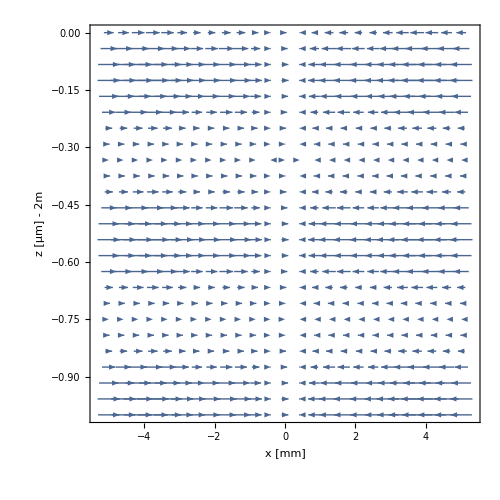

```mathematica
VectorPlot[aStark[10^-3 x,0,(10^-6 z)-2]⟦#⟧/.ev&/@{1,2}, {x,-5,5},{z,-1,0},  Frame->True,VectorPoints->25, PlotRange->All,VectorScale->0.09,ImageSize->500,FrameStyle->Directive[{Black, FontSize->16}],FrameLabel->{Style["x [mm]",FontWeight->Bold,FontSize->16,FontColor->Black],Style["z [µm] - 2m",FontWeight->Bold,FontSize->16,FontColor->Black]}]
```

## To 4.2.2: Divergence Calculation

### For TEM_00 Modes

This is calculating the total k vector as it is described in eq. 4.26 of the Master’s thesis.

```mathematica
k1=Grad[HGPhase[0,0,x,y,z-z0],{x,y,z}]/.ev;
k2=-Grad[HGPhase[0,0,x,y,-(z+z0)],{x,y,z}]/.ev;
k1v[x_,y_,z_]=k1;
k2v[x_,y_,z_]=k2;
BraggVector[x_/;x∈Reals,y_/;y∈Reals,z_/;z∈Reals]=Simplify[k1v[x,y,z]+k2v[x,y,z]];
```

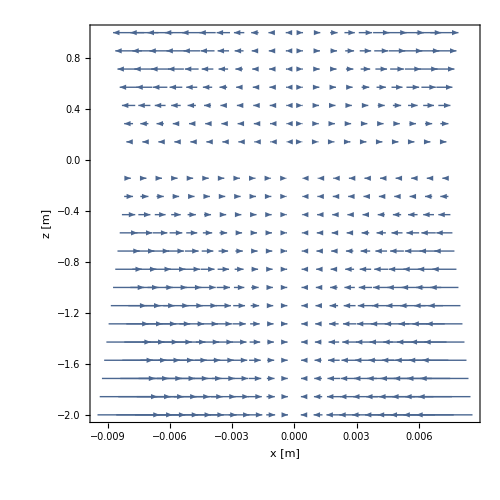

```mathematica
VectorPlot[BraggVector[x,0,z]⟦#⟧/.ev&/@{1,2}, {x,-0.008,0.008},{z,-2,1},ImageSize->500,Frame->True,FrameStyle->Directive[{Black, FontSize->16}],FrameLabel->{Style["x [m]",FontWeight->Bold,FontSize->16,FontColor->Black],Style["z [m]",FontWeight->Bold,FontSize->16,FontColor->Black]},VectorPoints->22, PlotRange->All,VectorScale->0.001]
```

This is calculating the angle of the resulting k vector using eq. 4.31 of the Master’s thesis.

```mathematica
θx[x_,y_,z_]:=Simplify[ArcTan[(BraggVector[x,y,z]⟦1⟧)/(BraggVector[x,y,z]⟦3⟧)]]
θy[x_,y_,z_]:=Simplify[ArcTan[(BraggVector[x,y,z]⟦2⟧)/(BraggVector[x,y,z]⟦3⟧)]]
```

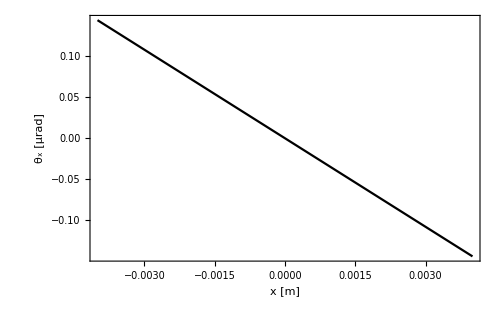

```mathematica
Plot[10^6 θx[x,0,-2]/.ev,{x,-0.004,0.004},PlotStyle->Black,ImageSize->500,Frame->True,FrameStyle->Directive[{Black, FontSize->18}],FrameLabel->{Style["x [m]",FontWeight->Bold,FontSize->18,FontColor->Black],Style["θ_x [µrad]",FontWeight->Bold,FontSize->18,FontColor->Black]},PlotRange->All]
```

### For Mixed Fields

This is calculating the resulting k vector for a field consisting of several Hermite-Gaussian modes using eq. 4.27-4.30 of the Master’s thesis. Because the Bragg beam is composed out of a multi-mode beam and its counter-propagating beam, this section uses the advantage that any complex number can be expressed in the form z=r e^(i ϕ). Because of that, it is possible to extract ϕ as follows. ETot is defined in the first chapter of this notebook.

```mathematica
NPhase[x_,y_,z_]=Re[-ⅈ Log[ETot[x,y,z]/Abs[ETot[x,y,z]]]]; (* Calculate phase using ϕ=-i log(z/r) *)
dx=10^-8; (* set stepsize for the numerical gradient calculation *)
dy=10^-8;
dz=10^-12;
NGrad[x_,y_,z_]:={(NPhase[x+dx,y,z]-NPhase[x-dx,y,z])/(2dx),(NPhase[x,y+dy,z]-NPhase[x,y-dy,z])/(2dy),(NPhase[x,y,z+dz]-NPhase[x,y,z-dz])/(2dz)}
```

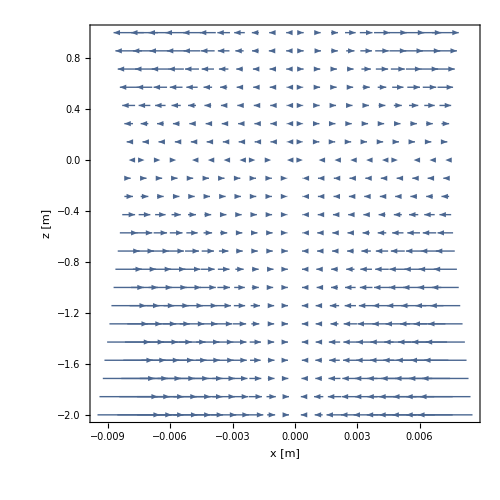

```mathematica
VectorPlot[NGrad[x,0,z]⟦#⟧/.ev&/@{1,2}, {x,-0.008,0.008},{z,-2,1},ImageSize->500,Frame->True,FrameStyle->Directive[{Black, FontSize->16}],FrameLabel->{Style["x [m]",FontWeight->Bold,FontSize->16,FontColor->Black],Style["z [m]",FontWeight->Bold,FontSize->16,FontColor->Black]},VectorPoints->22, PlotRange->All,VectorScale->0.001]
```

This is calculating the k vector angle as it is described in eq. 4.31.

```mathematica
nθx[x_,y_,z_]:=Simplify[ArcTan[(NGrad[x,y,z]⟦1⟧)/(NGrad[x,y,z]⟦3⟧)]]
nθy[x_,y_,z_]:=Simplify[ArcTan[(NGrad[x,y,z]⟦2⟧)/(NGrad[x,y,z]⟦3⟧)]]
```

## To 4.2.3: Interferometer Trajectories

### Height Function

#### Height Function for simultaneous conjugate Ramsey-Bordé interferometer (scrbi)

This subsection defines the height functions for the simultaneous conjugate Ramsey-Bordé interferometer of eq. 4.37 of the Master’s thesis. Here, Tp1 is T'_1 and Tp2 is T'_2.

```mathematica
(* The following numbers set the pulse separation times and Bloch pulse duration for the simultaneous conjugate Ramsey-Bordé geometry *)
T=0.08;
Tp1=0.015;
Tp2=0.015;
TBloch=0.008Sqrt[NBloch/125] ;
```

```mathematica
zfct[t_,b1_,b2_,b3_,o1_]=zoffset+Integrate[(v0+vph[nBragg](b1 HeavisideTheta[t]+b2 HeavisideTheta[t-T]+b3 HeavisideTheta[t-(T+Tp1+Tp2)]) +o1 vph[NBloch/2]HeavisideTheta[t-(T+Tp1)])-g t,t]/.ev
```

-2+1.51139×10^16 (2.97739×10^-16 t-3.23874×10^-16 t^2+1.85465×10^-19 b3 (-1.3823+12.5664 t) HeavisideTheta[-0.11+t]+3.7093×10^-20 o1 (-74.6128+785.398 t) HeavisideTheta[-0.095+t]-1.8645×10^-19 b2 HeavisideTheta[-0.08+t]+2.33062×10^-18 b2 t HeavisideTheta[-0.08+t]+2.33062×10^-18 b1 t HeavisideTheta[t])

```mathematica
(* Definition of the four individual height functions for the interferometer arms. *)
z1[t_]=zfct[t,0,1,1,1];
z2[t_]=zfct[t,1,0,0,1];
z3[t_]=zfct[t,1,-1,-1,-1];
z4[t_]=zfct[t,0,0,0,-1];
zlist={z1,z2,z3,z4};
```

#### Height Function for offset simultaneously conjugate interferometer (osci)

This subsection defines the height functions for the offset simultaneously conjugate interferometer of Fig. 2.4 of the Master’s thesis. Here, tTpmTp2 is T'-T'_2 and tTp2 is T'_2. tB1, tB2, and tB3 state the duration of the three Bloch pulses.

```mathematica
tTa=0.005;
tB1=0.008;
tTb=0.0376;
tB2=0.008;
tTc=0.1024;
tT=0.01;
tTpmTp2=0.005;
tB3=0.008;
tTp2=0.045;
```

```mathematica
oscizfct[t_,b1_,o1_,o2_,b2_,b3_,o3_,b4_]=zoffset+Integrate[(v0+vph[nBragg](b1 HeavisideTheta[t]+b2 HeavisideTheta[t-(tTa+tB1+tTb+tB2+tTc)]+b3 HeavisideTheta[t-(tTa+tB1+tTb+tB2+tTc+tT)]+b4 HeavisideTheta[t-(tTa+tB1+tTb+tB2+tTc+tT+tTpmTp2+tB3+tTp2)]) + vph[NBloch/2](o1 HeavisideTheta[t-tTa]+o2 HeavisideTheta[t-(tTa+tB1+tTb)]+o3 HeavisideTheta[t-(tTa+tB1+tTb+tB2+tTc+tT+tTpmTp2)])-g t),t]/.ev
```

-2+1.51139×10^16 (2.97739×10^-16 t-3.23874×10^-16 t^2+1.85465×10^-19 b4 (-2.8777+12.5664 t) HeavisideTheta[-0.229+t]+3.7093×10^-20 o3 (-138.23+785.398 t) HeavisideTheta[-0.176+t]-3.98537×10^-19 b3 HeavisideTheta[-0.171+t]+2.33062×10^-18 b3 t HeavisideTheta[-0.171+t]-3.7523×10^-19 b2 HeavisideTheta[-0.161+t]+2.33062×10^-18 b2 t HeavisideTheta[-0.161+t]-1.47412×10^-18 o2 HeavisideTheta[-0.0506+t]+2.91328×10^-17 o2 t HeavisideTheta[-0.0506+t]-1.45664×10^-19 o1 HeavisideTheta[-0.005+t]+2.91328×10^-17 o1 t HeavisideTheta[-0.005+t]+2.33062×10^-18 b1 t HeavisideTheta[t])

```mathematica
zB1[t_]=oscizfct[t,0,0,0,0,1,1,1];
zB2[t_]=oscizfct[t,0,0,0,1,0,1,0];
zC1[t_]=oscizfct[t,1,1,-1,-1,0,-1,0];
zC2[t_]=oscizfct[t,1,1,-1,0,-1,-1,-1];
oscizlist={zB1,zB2,zC1,zC2};
```

### Modules for Different Processes and AI Configurations

Definition of the modules as they are described as part of the thesis, i.e. eq. 4.23, 4.32 and 4.34.

```mathematica
Bragg[tprop_,zfun_,{x0_,y0_,vx0_,vy0_,ttotal_}]:=
Module[{x=x0,y=y0,vx=vx0,vy=vy0,Ttotal=ttotal},
vBraggx=(vph[nBragg]/.ev) θx[x,y,zfun[Ttotal]/.ev]/.ev;
vBraggy=(vph[nBragg]/.ev) θy[x,y,zfun[Ttotal]/.ev]/.ev;
vx=vx+vBraggx;
vy=vy+vBraggy;
x=x+vx tprop;
y=y+vy tprop;
Ttotal=Ttotal+tprop;
{x,y,vx,vy,Ttotal}
]
```

```mathematica
Propagate[tprop_,{x0_,y0_,vx0_,vy0_,ttotal_}]:=
Module[{x=x0,y=y0,vx=vx0,vy=vy0,Ttotal=ttotal},
{x=x+vx tprop,y=y+vy tprop,Ttotal=Ttotal+tprop} ;
{x,y,vx,vy,Ttotal}
]
```

```mathematica
Bloch[tprop_,zfun_,{x0_,y0_,vx0_,vy0_,ttotal_}]:=
Module[{x=x0,y=y0,vx=vx0,vy=vy0,Ttotal=ttotal},
aBlochx=aStarkAverage[x,y,zfun[Ttotal]]⟦1⟧;aBlochy=aStarkAverage[x,y,zfun[Ttotal]]⟦2⟧;x=x+vx tprop+1/2 aBlochx tprop^2;y=y+vy tprop+1/2 aBlochy tprop^2;vx=vx+aBlochx tprop;vy=vy+aBlochy tprop;Ttotal=Ttotal+tprop ;
{x,y,vx,vy,Ttotal}
]
```

```mathematica
BlochnSteps[tprop_,nSteps_,zfun_,{x0_,y0_,vx0_,vy0_,ttotal_}]:=
Module[{x=x0,y=y0,vx=vx0,vy=vy0,Ttotal=ttotal},For[i=0,i<nSteps,i++,{x,y,vx,vy,Ttotal}=Bloch[tprop/nSteps,zfun,{x,y,vx,vy,Ttotal}];];{x,y,vx,vy,Ttotal}];
```

The following two cells are the combined modules for the entire scrbi and osci geometries.

```mathematica
Clear[scrbi]
scrbi[zfun_,{x0_,y0_,vx_,vy_},tprop1_,tprop2_,tprop3_,tBloch_,tafterBloch_]:=
Bragg[tprop3,zfun,Propagate[tafterBloch,BlochnSteps[tBloch,4,zfun,Bragg[tprop2,zfun,Bragg[tprop1,zfun,{x0,y0,vx,vy,0}]/.ev]/.ev]/.ev]/.ev]/.ev
```

```mathematica
osci[zfun_,{x0_,y0_,vx_,vy_},tTa_,tTb_,tTc_,tT_,tTpmTp2_,tTp2_,tB1_,tB2_,tB3_]:=
Bragg[tT,zfun,Propagate[tTp2,BlochnSteps[tB3,4,zfun,Bragg[tTpmTp2,zfun,Bragg[tT,zfun,Propagate[tTc,BlochnSteps[tB2,4,zfun,Propagate[tTb,BlochnSteps[tB1,4,zfun,Bragg[tTa,zfun,{x0,y0,vx,vy,0}]/.ev]/.ev]/.ev]/.ev]/.ev]/.ev]/.ev]/.ev]]/.ev
```

## To 4.2.4: Contrast Calculation

This section simulates the atoms, runs them over the scrbi or osci modules and saves the results as x_(f,i) as described in the thesis. From there, it is calculating the mean displacement (which is more for personal interest) and the interferometer contrast.

### Atom Generation

Generate the number of atoms NAtoms, where position and velocity have bivariate normal distribution with σ_(x,y)=2.2mm and σ_v=1.5 v_r=1.5  ℏk/m.

```mathematica
σx=0.0022;
σy=0.0022;
vr=vph[0.5]/.ev;
σv=1.5 vr;
NAtoms=100;
```

```mathematica
ASP=RandomVariate[BinormalDistribution[{σx,σy},0],NAtoms];
ASV=RandomVariate[BinormalDistribution[{σv,σv},0],NAtoms];
```

```mathematica
start=Table[{ASP⟦i,1⟧,ASP⟦i,2⟧,ASP⟦i,1⟧,ASP⟦i,2⟧},{i,NAtoms}];
```

```mathematica
LaunchKernels[4]
```

{KernelObject[1,local],KernelObject[2,local],KernelObject[3,local],KernelObject[4,local]}

```mathematica
enddata=ParallelTable[Table[scrbi[zlist⟦j⟧,Flatten[start⟦i⟧],T,Tp1,T,TBloch,Tp2],{i,NAtoms}],{j,4}];
(*enddata=ParallelTable[Table[osci[oscizlist⟦j⟧,Flatten[start⟦i⟧],tTa,tTb,tTc,tT,tTpmTp2,tTp2,tB1,tB2,tB3],{i,NAtoms}],{j,2}]*)
```

```mathematica
Subscript[x, f,1]=Table[{enddata⟦1,i,1⟧,enddata⟦1,i,2⟧},{i,NAtoms}];
Subscript[x, f,2]=Table[{enddata⟦2,i,1⟧,enddata⟦2,i,2⟧},{i,NAtoms}];
Subscript[x, f,3]=Table[{enddata⟦3,i,1⟧,enddata⟦3,i,2⟧},{i,NAtoms}];
Subscript[x, f,4]=Table[{enddata⟦4,i,1⟧,enddata⟦4,i,2⟧},{i,NAtoms}];
UI=Table[{{Subscript[x, f,1]⟦i,1⟧,Subscript[x, f,1]⟦i,2⟧},{Subscript[x, f,2]⟦i,1⟧,Subscript[x, f,2]⟦i,2⟧}},{i,NAtoms}];
LI=Table[{{Subscript[x, f,3]⟦i,1⟧,Subscript[x, f,3]⟦i,2⟧},{Subscript[x, f,4]⟦i,1⟧,Subscript[x, f,4]⟦i,2⟧}},{i,NAtoms}];
```

#### Density Plots

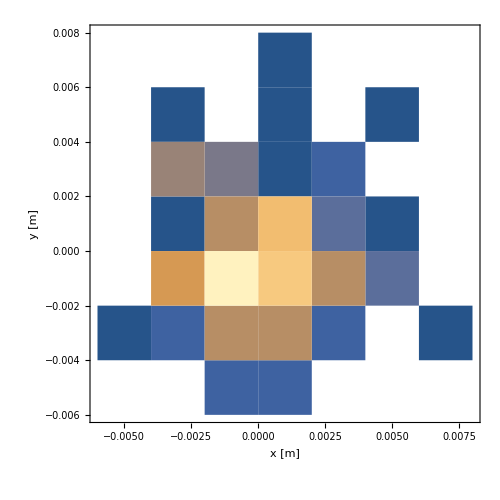

```mathematica
DensityHistogram[ASP,ImageSize->500,FrameStyle->Directive[{Black, FontSize->16}],FrameLabel->{Style["x [m]",FontWeight->Bold,FontSize->16,FontColor->Black],Style["y [m]",FontWeight->Bold,FontSize->16,FontColor->Black]}]
```

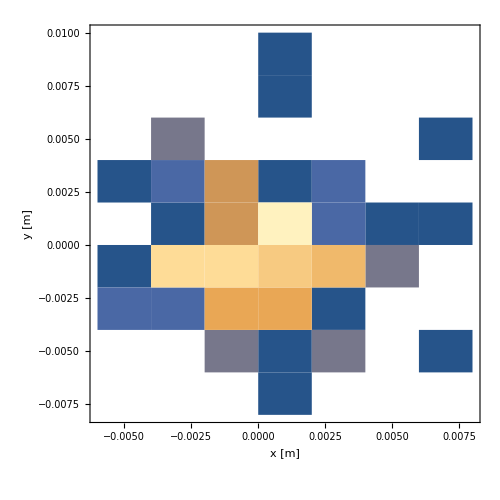

```mathematica
(* Density plot of the atom position distribution *)
DensityHistogram[Subscript[x, f,1],ImageSize->500,FrameStyle->Directive[{Black, FontSize->16}],FrameLabel->{Style["x [m]",FontWeight->Bold,FontSize->16,FontColor->Black],Style["y [m]",FontWeight->Bold,FontSize->16,FontColor->Black]}]
```

### Contrast Calculation

Here is the explicit contrast calculation using eq. 4.38 and 4.39.

```mathematica
(* Definition of the contrast the way it is described in the thesis *)
λdB=270 10^-9;
contrast[δx_]:=Exp[-δx^2/(4 λdB^2)]
```

#### Contrast Radial

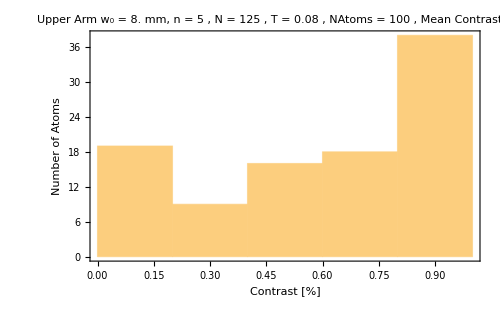

The mean contrast in radial direction for the upper interferometer is: 0.600289

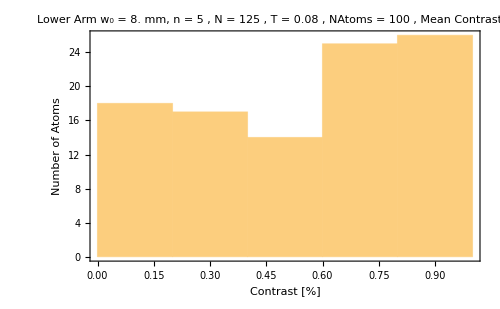

The mean contrast in radial direction for the lower interferometer is: 0.571976

```mathematica
Clear[contrastupperarmr]
contrastupperarmr=Table[contrast[√((Subscript[x, f,1]⟦i,1⟧-Subscript[x, f,2]⟦i,1⟧)^2+(Subscript[x, f,1]⟦i,2⟧-Subscript[x, f,2]⟦i,2⟧)^2)],{i,Length[Subscript[x, f,2]]}];
h1=Histogram[contrastupperarmr,Frame->True,ImageSize->500,FrameStyle->Directive[{Black, FontSize->16}],FrameLabel->{Style["Contrast",FontWeight->Bold,FontSize->16,FontColor->Black],Style["Number of Atoms",FontWeight->Bold,FontSize->16,FontColor->Black]},PlotLabel->Style[StringForm["Upper Arm \n w_0 = `` mm, n = `` , N = `` , T = `` , NAtoms = `` , Mean Contrast `` %",10^3 w0/.ev, nBragg/.ev,NBloch,T,NAtoms,Round[100Mean[contrastupperarmr]]],FontWeight->Bold,FontSize->12,FontColor->Black]]
Print["The mean contrast in radial direction for the upper interferometer is: ",Mean[contrastupperarmr]]
Clear[contrastlowerarmr]
contrastlowerarmr=Table[contrast[√((Subscript[x, f,3]⟦i,1⟧-Subscript[x, f,4]⟦i,1⟧)^2+(Subscript[x, f,3]⟦i,2⟧-Subscript[x, f,4]⟦i,2⟧)^2)],{i,Length[Subscript[x, f,3]]}];
h2=Histogram[contrastlowerarmr,Frame->True,ImageSize->500,FrameStyle->Directive[{Black, FontSize->16}],FrameLabel->{Style["Contrast",FontWeight->Bold,FontSize->16,FontColor->Black],Style["Number of Atoms",FontWeight->Bold,FontSize->16,FontColor->Black]},PlotLabel->Style[StringForm["Lower Arm \n w_0 = `` mm, n = `` , N = `` , T = `` , NAtoms = `` , Mean Contrast `` %",10^3 w0/.ev, nBragg/.ev,NBloch,T,NAtoms,Round[100Mean[contrastlowerarmr]]],FontWeight->Bold,FontSize->12,FontColor->Black]]
Print["The mean contrast in radial direction for the lower interferometer is: ",Mean[contrastlowerarmr]]
```

### Radius Dependence of Contrast

This generates the plots such as the ones in Fig. 4.13.

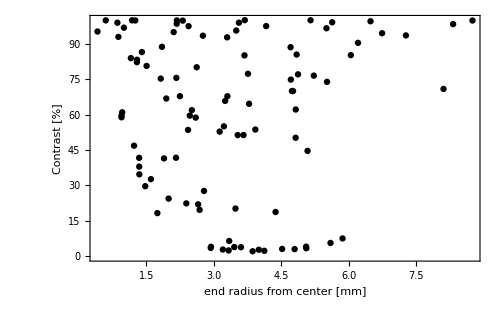

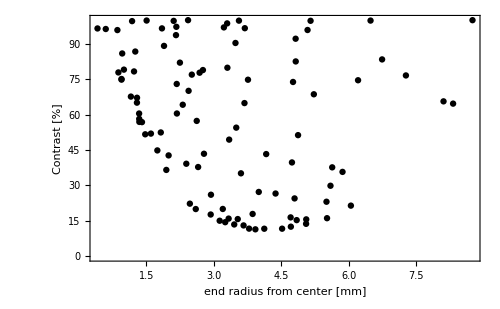

```mathematica
ListPlot[Table[{10^3 √(((Subscript[x, f,1]⟦i,1⟧+Subscript[x, f,2]⟦i,1⟧)/2)^2+((Subscript[x, f,1]⟦i,2⟧+Subscript[x, f,2]⟦i,2⟧)/2)^2),100contrast[√((Subscript[x, f,1]⟦i,1⟧-Subscript[x, f,2]⟦i,1⟧)^2+(Subscript[x, f,1]⟦i,2⟧-Subscript[x, f,2]⟦i,2⟧)^2)]},{i,NAtoms}],ImageSize->500,Frame->True,PlotStyle->Black,FrameStyle->Directive[{Black, FontSize->18}],FrameLabel->{Style["end radius from center [mm]",FontWeight->Bold,FontSize->18,FontColor->Black],Style["Contrast [%]",FontWeight->Bold,FontSize->18,FontColor->Black]},PlotRange->All]
ListPlot[Table[{10^3 √(((Subscript[x, f,3]⟦i,1⟧+Subscript[x, f,4]⟦i,1⟧)/2)^2+((Subscript[x, f,3]⟦i,2⟧+Subscript[x, f,4]⟦i,2⟧)/2)^2),100 contrast[√((Subscript[x, f,3]⟦i,1⟧-Subscript[x, f,4]⟦i,1⟧)^2+(Subscript[x, f,3]⟦i,2⟧-Subscript[x, f,4]⟦i,2⟧)^2)]},{i,NAtoms}],ImageSize->500,Frame->True,PlotStyle->Black,FrameStyle->Directive[{Black, FontSize->18}],FrameLabel->{Style["end radius from center [mm]",FontWeight->Bold,FontSize->18,FontColor->Black],Style["Contrast [%]",FontWeight->Bold,FontSize->18,FontColor->Black]},PlotRange->All]
```

### Contrast with Radius Cutoff

This calculates and plots the contrast only of atoms that are less than 2.5 mm away from the center (x,y=0).

```mathematica
Clear[UIwCO]
UIwCO=Select[UI,√((#⟦1,1⟧)^2+(#⟦1,2⟧)^2)<0.0025&];
Clear[LIwCO]
LIwCO=Select[LI,√((#⟦1,1⟧)^2+(#⟦1,2⟧)^2)<0.0025&];
```

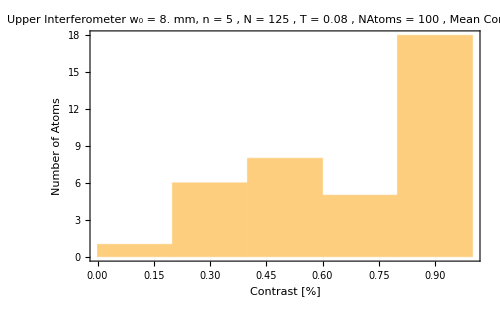

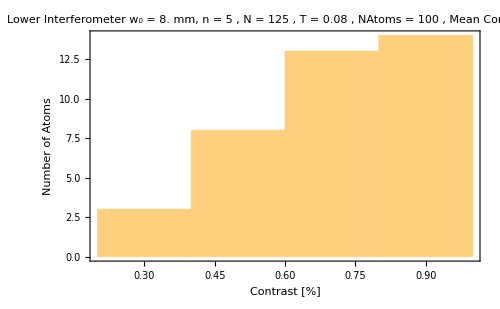

```mathematica
contrastUIwCO=Table[contrast[√((UIwCO⟦i,1,1⟧-UIwCO⟦i,2,1⟧)^2+(UIwCO⟦i,1,2⟧-UIwCO⟦i,2,2⟧)^2)],{i,Length[UIwCO]}];
histUIwCO=Histogram[contrastUIwCO,Frame->True,ImageSize->500,FrameStyle->Directive[{Black, FontSize->16}],FrameLabel->{Style["Contrast",FontWeight->Bold,FontSize->16,FontColor->Black],Style["Number of Atoms",FontWeight->Bold,FontSize->16,FontColor->Black]},PlotLabel->Style[StringForm["Upper Interferometer \n w_0 = `` mm, n = `` , N = `` , T = `` , NAtoms = `` , Mean Contrast `` %",10^3 w0/.ev, nBragg/.ev,NBloch,T,NAtoms,Round[100Mean[contrastUIwCO]]],FontWeight->Bold,FontSize->12,FontColor->Black]]
contrastLIwCO=Table[contrast[√((LIwCO⟦i,1,1⟧-LIwCO⟦i,2,1⟧)^2+(LIwCO⟦i,1,2⟧-LIwCO⟦i,2,2⟧)^2)],{i,Length[LIwCO]}];
histLIwCO=Histogram[contrastLIwCO,Frame->True,ImageSize->500,FrameStyle->Directive[{Black, FontSize->16}],FrameLabel->{Style["Contrast",FontWeight->Bold,FontSize->16,FontColor->Black],Style["Number of Atoms",FontWeight->Bold,FontSize->16,FontColor->Black]},PlotLabel->Style[StringForm["Lower Interferometer \n w_0 = `` mm, n = `` , N = `` , T = `` , NAtoms = `` , Mean Contrast `` %",10^3 w0/.ev, nBragg/.ev,NBloch,T,NAtoms,Round[100Mean[contrastLIwCO]]],FontWeight->Bold,FontSize->12,FontColor->Black]]
```